```mathematica
CoeffiMat[n_]:= {
{r[n]^(m[1,n]-2),r[n]^(m[2,n]-2),r[n]^(m[3,n]-2),r[n]^(m[4,n]-2)}
,{g[1,n] r[n]^(m[1,n]-2),g[2,n] r[n]^(m[2,n]-2),g[3,n] r[n]^(m[3,n]-2),g[4,n] r[n]^(m[4,n]-2)}
,{r[n-1]^(m[1,n]-2),r[n-1]^(m[2,n]-2),r[n-1]^(m[3,n]-2),r[n-1]^(m[4,n]-2)}
,{g[1,n] r[n-1]^(m[1,n]-2),g[2,n]  r[n-1]^(m[2,n]-2),g[3,n] r[n-1]^(m[3,n]-2),g[4,n] r[n-1]^(m[4,n]-2)}}
μMat[n_]:={-μ[1,n],-μ[2,n],-μ[1,n],-μ[2,n]}
ΚMat[n_] := LinearSolve[CoeffiMat[n],μMat[n]]
```

```mathematica
Νl
```

2

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
BMat[n_]:={
{r[n-1]^m[1,n-1],r[n-1]^m[2,n-1],r[n-1]^m[3,n-1],r[n-1]^m[4,n-1]}
,{g[1,n-1] r[n-1]^m[1,n-1],g[2,n-1] r[n-1]^m[2,n-1],g[3,n-1] r[n-1]^m[3,n-1],g[4,n-1] r[n-1]^m[4,n-1]}
,{Q[1,n-1] r[n-1]^m[1,n-1],Q[2,n-1] r[n-1]^m[2,n-1],Q[3,n-1] r[n-1]^m[3,n-1],Q[4,n-1] r[n-1]^m[4,n-1]}
,{W[1,n-1] r[n-1]^m[1,n-1],W[2,n-1]  r[n-1]^m[2,n-1],W[3,n-1] r[n-1]^m[3,n-1],W[4,n-1] r[n-1]^m[4,n-1]}}
AMat[n_]:={
{r[n-1]^m[1,n],r[n-1]^m[2,n],r[n-1]^m[3,n],r[n-1]^m[4,n]}
,{g[1,n] r[n-1]^m[1,n],g[2,n] r[n-1]^m[2,n],g[3,n] r[n-1]^m[3,n],g[4,n] r[n-1]^m[4,n]}
,{Q[1,n] r[n-1]^m[1,n],Q[2,n] r[n-1]^m[2,n],Q[3,n] r[n-1]^m[3,n],Q[4,n] r[n-1]^m[4,n]}
,{W[1,n] r[n-1]^m[1,n],W[2,n]  r[n-1]^m[2,n],W[3,n] r[n-1]^m[3,n],W[4,n] r[n-1]^m[4,n]}}
DMat[n_]:=-r[n-1]^2{μ[1,n]-μ[1,n-1],μ[2,n]-μ[2,n-1],Q[5,n]-Q[5,n-1],W[5,n]-W[5,n-1]}
```

```mathematica
ABMat = ConstantArray[0.0,{4*Νl,4*Νl}];
DDMat = ConstantArray[0.0,4*Νl];
ABMat[[1;;2,1;;4]]=r[0]^2 CoeffiMat[1][[3;;4,1;;4]];
ABMat[[-2;;-1,-4;;-1]]=r[Νl]^2 CoeffiMat[Νl][[1;;2,1;;4]];
DDMat[[1;;2]]=r[0]^2{μ[1,1],μ[2,1]};
DDMat[[-2;;-1]]=r[Νl]^2{μ[1,Νl],μ[2,Νl]};
Do[
row = 2+(n-2)*4;
colB = (n-2)*4;
colA = (n-1)*4;
ABMat[[(row+1);;(row+4),(colB+1);;(colB+4)]]=BMat[n];
ABMat[[(row+1);;(row+4),(colA+1);;(colA+4)]]=-AMat[n];
DDMat[[(row+1);;(row+4)]] = DMat[n]
,{n,2,Νl}];
KKMat =LinearSolve[ABMat,DDMat];
```

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{0.,0.,0.,0.,0.,0.,0.,0.}

{{2.09116×10^-6,0.0000867718,478204.,11524.5},{1.13245×10^-6,-0.000349459,84276.8,-15554.1}}

{{0.0000141183,0.00119615,70829.9,836.014},{-0.0000163504,0.00232095,-37733.7,668.792}}

{-88233.,-9173.91}

{-1.53028×10^6,152023.}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.},{0.0000386669,0.000698885,«4»,-306244.,-2019.8},{«1»},«1»,{5.95708×10^-15,«6»,«22»},{0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

{-3.39603×10^10,-8.42367×10^7,-0.0185346,-0.0905908,-7.13357×10^10,-4.14592×10^8,0.321194,-59.7776}

```mathematica
KKMat[[i+(n-1)*4]]
```

{-3.39603×10^10,-8.42367×10^7,-0.0185346,-0.0905908,-7.13357×10^10,-4.14592×10^8,0.321194,-59.7776}

```mathematica
Κ[i_,n_]:=KKMat[[i+(n-1)*4]]
```

```mathematica
BMat[2]//MatrixForm
AMat[2]//MatrixForm
```

(0.0000386669 | 0.000698885 | 25861.9 | 1430.85
0.0000209397 | -0.00281464 | 4557.8 | -1931.16
1.22589×10^-14 | 2.61698×10^-13 | -3.32987×10^-6 | -1.47536×10^-7
5.95708×10^-15 | -8.74824×10^-13 | -1.81477×10^-6 | 5.60718×10^-7)

(3.26537×10^-6 | 0.000495098 | 306244. | 2019.8
-3.78161×10^-6 | 0.000960663 | -163148. | 1615.8
8.69155×10^-16 | 1.89545×10^-13 | -0.0000411383 | -2.45665×10^-7
-7.77685×10^-16 | 2.47436×10^-13 | 0.0000396037 | -3.44066×10^-7)

```mathematica
ABMat//MatrixForm
```

(2.09116×10^-6 | 0.0000867718 | 478204. | 11524.5 | 0. | 0. | 0. | 0.
1.13245×10^-6 | -0.000349459 | 84276.8 | -15554.1 | 0. | 0. | 0. | 0.
0.0000386669 | 0.000698885 | 25861.9 | 1430.85 | -3.26537×10^-6 | -0.000495098 | -306244. | -2019.8
0.0000209397 | -0.00281464 | 4557.8 | -1931.16 | 3.78161×10^-6 | -0.000960663 | 163148. | -1615.8
1.22589×10^-14 | 2.61698×10^-13 | -3.32987×10^-6 | -1.47536×10^-7 | -8.69155×10^-16 | -1.89545×10^-13 | 0.0000411383 | 2.45665×10^-7
5.95708×10^-15 | -8.74824×10^-13 | -1.81477×10^-6 | 5.60718×10^-7 | 7.77685×10^-16 | -2.47436×10^-13 | -0.0000396037 | 3.44066×10^-7
0. | 0. | 0. | 0. | 0.0000141183 | 0.00119615 | 70829.9 | 836.014
0. | 0. | 0. | 0. | -0.0000163504 | 0.00232095 | -37733.7 | 668.792)

```mathematica
DMat[2]//MatrixForm
DDMat//MatrixForm
```

(-912044.
-196423.
-0.000299171
-0.000114809)

(-88233.
-9173.91
-912044.
-196423.
-0.000299171
-0.000114809
-1.53028×10^6
152023.)

```mathematica
list3 = EIofN3/@Range[2,100]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.},«8»,{0.,0.,0.,0.,0.,0.,0.,0.,0.000125539,0.00162236,7965.63,616.384},{0.,0.,0.,0.,0.,0.,0.,0.,0.0000679847,-0.00653379,1403.83,-831.91}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«12»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{707.714,1085.79,906.068,1093.12,961.572,1086.94,986.388,1081.05,1000.23,1076.39,1009.,1072.75,1015.03,1069.88,1019.42,1067.56,1022.76,1065.65,1025.38,1064.07,1027.5,1062.72,1029.23,1061.57,1030.69,1060.58,1031.92,1059.71,1032.98,1058.94,1033.9,1058.26,1034.71,1057.66,1035.42,1057.11,1036.06,1056.62,1036.63,1056.17,1037.14,1055.76,1037.6,1055.39,1038.03,1055.04,1038.41,1054.73,1038.77,1054.43,1039.09,1054.16,1039.39,1053.91,1039.67,1053.67,1039.93,1053.45,1040.17,1053.25,1040.39,1053.05,1040.61,1052.87,1040.8,1052.7,1040.99,1052.54,1041.16,1052.38,1041.33,1052.24,1041.48,1052.1,1041.63,1051.97,1041.77,1051.85,1041.9,1051.73,1042.03,1051.62,1042.15,1051.51,1042.26,1051.41,1042.37,1051.31,1042.47,1051.22,1042.57,1051.13,1042.67,1051.04,1042.76,1050.96,1042.84,1050.88,1042.93}

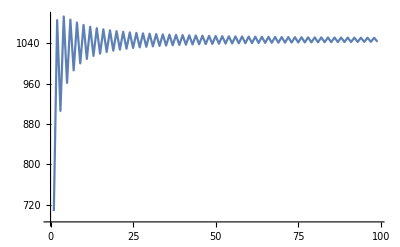

```mathematica
ListLinePlot[list3,PlotRange->All]
```

```mathematica
ListLinePlot[Κ[1,#]&/@Range[100],PlotRange->All]
ListLinePlot[Κ[2,#]&/@Range[100],PlotRange->All]
ListLinePlot[Κ[3,#]&/@Range[100],PlotRange->All]
ListLinePlot[Κ[4,#]&/@Range[100],PlotRange->All]
```

```mathematica
Κ[1,2]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

5.12784×10^10

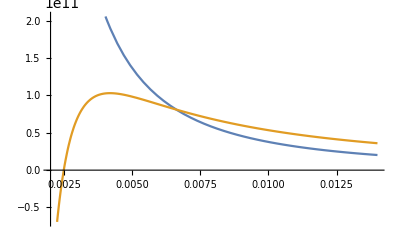

```mathematica
Plot[{Evaluate[Κ[1,1,x]],Evaluate[Κ[1,2,x]]},{x,2*10^-3,14*10^-3}]
```

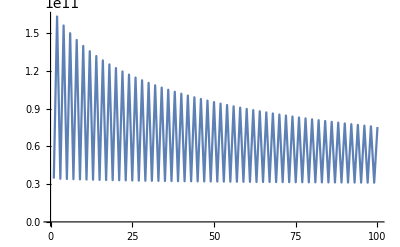

-Graphics-

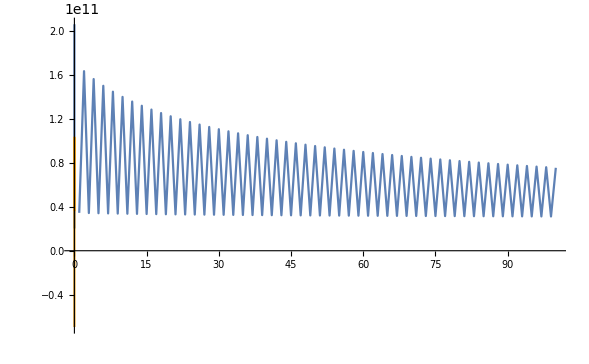

```mathematica
Show[,,PlotRange->All
]
```

```mathematica
list4 = EIofN3/@Range[2,10]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.},«8»,{0.,0.,0.,0.,0.,0.,0.,0.,0.000125539,0.00162236,7965.63,616.384},{0.,0.,0.,0.,0.,0.,0.,0.,0.0000679847,-0.00653379,1403.83,-831.91}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«12»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{707.714,1085.79,906.068,1093.12,961.572,1086.94,986.388,1081.05,1000.23}

```mathematica
Inverse[Abar[2]].Abar[2]//Chop//MatrixForm
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
GMat0[1]
GMat0[2]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{4.9342×10^8,-6.81422×10^8,3.73868×10^8,2.81173×10^9}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{3.8414×10^8,-1.14789×10^8,-9.32814×10^8,3.53005×10^9}

```mathematica
Κ[i_,n_,x_]:=x^(-m[i,n])(GMat0[n][[i]] x^2+Sum[GMat[n][[i,j]] x^(Λ[n][[j]]),{j,4}])
```

```mathematica
KeMat[n_,t_]:=Simplify[Inverse[MνMat[n]].YMat[n,t]/.Solsc[n][[1]]]
```

```mathematica
Κ2[i_,n_,x_]:=x^(-m[i,n])KeMat[n,x][[i]]
```

```mathematica
Κ[4,1,14*10^-3]-Κ2[4,1,14*10^-3]//Simplify
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

-1.25056×10^-12

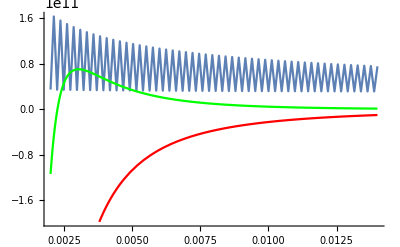

```mathematica
Show[ListLinePlot[Κ[1,#]&/@Range[Νl],DataRange->{2*10^-3,14*10^-3}],Plot[{Evaluate[Κ[1,1,x]],Evaluate[Κ[1,2,x]]},{x,2*10^-3,14*10^-3},PlotStyle->{Red,Green}],PlotRange->All]
```

```mathematica
r/@Range[1,100,2]//N
```

{0.00212,0.00236,0.0026,0.00284,0.00308,0.00332,0.00356,0.0038,0.00404,0.00428,0.00452,0.00476,0.005,0.00524,0.00548,0.00572,0.00596,0.0062,0.00644,0.00668,0.00692,0.00716,0.0074,0.00764,0.00788,0.00812,0.00836,0.0086,0.00884,0.00908,0.00932,0.00956,0.0098,0.01004,0.01028,0.01052,0.01076,0.011,0.01124,0.01148,0.01172,0.01196,0.0122,0.01244,0.01268,0.01292,0.01316,0.0134,0.01364,0.01388}

```mathematica
m[#,1]&/@Range[4]
```

{2.10436,1.50488,-2.10436,-1.50488}

```mathematica
m[1,1]
Λ[1]
```

2.10436

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

{-0.911336,0.911336,0.564217,-0.564217}

```mathematica
lm=LinearModelFit[data,{t^(2-m[1,1]),t^(Λ[1][[1]]-m[1,1]),t^(Λ[1][[2]]-m[1,1]),t^(Λ[1][[3]]-m[1,1]),t^(Λ[1][[4]]-m[1,1])},t]
lm//Normal
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

FittedModel[1.61751×10^10-7.86965/t^3.0157+(«16»)/t^(«18»)-(«19»)/t^(«19»)+927107./t^(«18»)+(9.52021×10^9)/t^0.104363]

1.61751×10^10-7.86965/t^3.0157+98.9917/t^2.66858-132201./t^1.54015+927107./t^1.19303+(9.52021×10^9)/t^0.104363

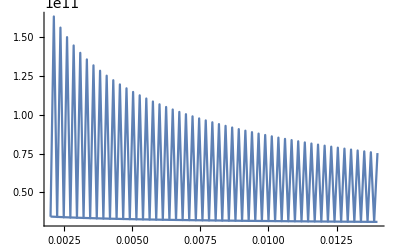

```mathematica
Show[ListLinePlot[Κ[1,#]&/@Range[Νl],DataRange->{2*10^-3,14*10^-3}],Plot[lm[x],{x,2*10^-3,14*10^-3}],PlotRange->All]
```

```mathematica
data = Transpose[{r/@Range[1,100,2]//N,Κ[1,#]&/@Range[1,100,2]}]
```

{{0.00212,3.44169×10^10},{0.00236,3.42224×10^10},{0.0026,3.4044×10^10},{0.00284,3.38805×10^10},{0.00308,3.37302×10^10},{0.00332,3.35915×10^10},{0.00356,3.34629×10^10},{0.0038,3.33431×10^10},{0.00404,3.32313×10^10},{0.00428,3.31263×10^10},{0.00452,3.30276×10^10},{0.00476,3.29344×10^10},{0.005,3.28462×10^10},{0.00524,3.27626×10^10},{0.00548,3.2683×10^10},{0.00572,3.26072×10^10},{0.00596,3.25347×10^10},{0.0062,3.24655×10^10},{0.00644,3.23991×10^10},{0.00668,3.23354×10^10},{0.00692,3.22742×10^10},{0.00716,3.22153×10^10},{0.0074,3.21585×10^10},{0.00764,3.21038×10^10},{0.00788,3.20509×10^10},{0.00812,3.19997×10^10},{0.00836,3.19502×10^10},{0.0086,3.19023×10^10},{0.00884,3.18558×10^10},{0.00908,3.18107×10^10},{0.00932,3.1767×10^10},{0.00956,3.17244×10^10},{0.0098,3.1683×10^10},{0.01004,3.16428×10^10},{0.01028,3.16036×10^10},{0.01052,3.15654×10^10},{0.01076,3.15281×10^10},{0.011,3.14918×10^10},{0.01124,3.14563×10^10},{0.01148,3.14217×10^10},{0.01172,3.13879×10^10},{0.01196,3.13548×10^10},{0.0122,3.13225×10^10},{0.01244,3.12909×10^10},{0.01268,3.12599×10^10},{0.01292,3.12296×10^10},{0.01316,3.11999×10^10},{0.0134,3.11708×10^10},{0.01364,3.11423×10^10},{0.01388,3.11144×10^10}}

-Graphics-

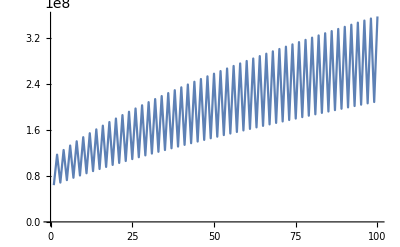

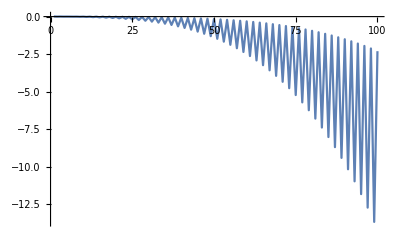

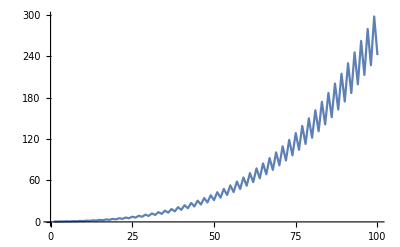

```mathematica
ListLinePlot[Κ[1,#]&/@Range[Νl],PlotRange->All]
ListLinePlot[Κ[2,#]&/@Range[Νl],PlotRange->All]
ListLinePlot[Κ[3,#]&/@Range[Νl],PlotRange->All]
ListLinePlot[Κ[4,#]&/@Range[Νl],PlotRange->All]
```

```mathematica
Κ[i_,n_,x_]:=x^(-m[i,n])(GMat0[n][[i]] x^2+Sum[GMat[n][[i,j]] x^(Λ[n][[j]]),{j,4}])
```

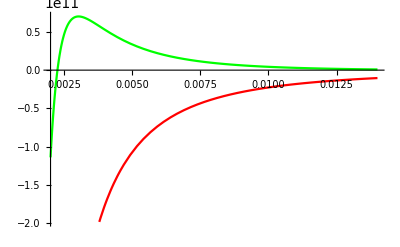

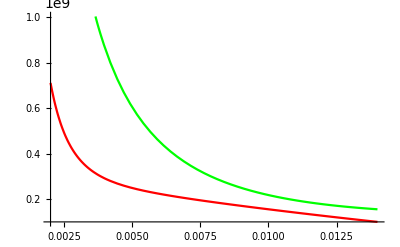

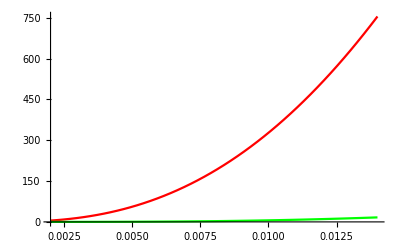

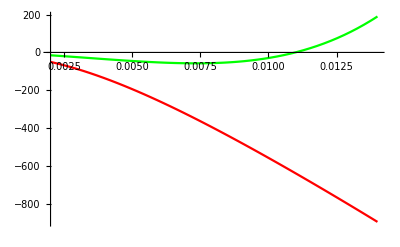

-Graphics-

```mathematica
Plot[{Evaluate[Κ[1,1,x]],Evaluate[Κ[1,2,x]]},{x,2*10^-3,14*10^-3},PlotStyle->{Red,Green}]
Plot[{Evaluate[Κ[2,1,x]],Evaluate[Κ[2,2,x]]},{x,2*10^-3,14*10^-3},PlotStyle->{Red,Green}]
Plot[{Evaluate[Κ[3,1,x]],Evaluate[Κ[3,2,x]]},{x,2*10^-3,14*10^-3},PlotStyle->{Red,Green}]
Plot[{Evaluate[Κ[4,1,x]],Evaluate[Κ[4,2,x]]},{x,2*10^-3,14*10^-3},PlotStyle->{Red,Green}]
```

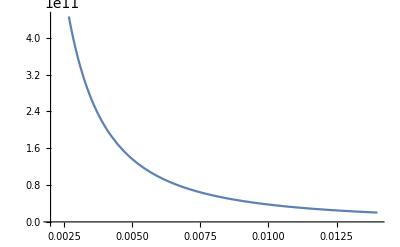

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

5.49388×10^11

```mathematica
Plot[-557.6585785122379/x^3.0156993066412268+21648.00004252886/x^2.6685803484741446+(4.73867987250147*^7)/x^1.5401460139522667-(9.944415884932022*^7)/x^1.1930270557851825+(4.9342035093632793*^8)/x^0.10436318121320554,{x,2*10^-3,14*10^-3}]
```

```mathematica
GMat[1]-GMat[2]
```

{{-1.42627×10^8,-619.407,22793.6,5.2277×10^7},{8.96797×10^6,-543.792,10578.4,-3.30907×10^6},{7.67543×10^7,1455.83,-68841.1,-9.5875×10^6},{1.49296×10^8,-698.1,20375.7,-2.75239×10^7}}

```mathematica
LMat[1]/(2-Λ[1])
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

```mathematica
c1
```

c1

```mathematica
t*D[YMat[1,t],t]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{(-(0.911336 c1)/t^1.91134-1.60452×10^9 t) t,((0.911336 c2)/t^0.0886639-4.292×10^9 t) t,((0.564217 c3)/t^0.435783-4.29752×10^9 t) t,(-(0.564217 c4)/t^1.56422-1.83469×10^9 t) t}

```mathematica
ClearAll[Solsc,KeMat]
```

```mathematica
eq1 =Simplify[Total[Inverse[MνMat[1]].YMat[1,r0]]]==-r0^2 μ[1,1];
eq2 = Simplify[(Inverse[MνMat[1]].YMat[1,r0]).{g[1,1],g[2,1],g[3,1],g[4,1]}]==-r0^2 μ[2,1];
eq3 =Simplify[ Total[Inverse[MνMat[1]].YMat[1,rN]]]==-rN^2 μ[1,1];
eq4 = Simplify[(Inverse[MνMat[1]].YMat[1,rN]).{g[1,1],g[2,1],g[3,1],g[4,1]}]==-rN^2 μ[2,1];
Solsc[1]=NSolve[eq1&&eq2&&eq3&&eq4,{c1,c2,c3,c4}];
eq1 =Simplify[ Total[Inverse[MνMat[2]].YMat[2,r0]]]==-r0^2 μ[1,2];
eq2 = Simplify[(Inverse[MνMat[2]].YMat[2,r0]).{g[1,2],g[2,2],g[3,2],g[4,2]}]==-r0^2 μ[2,2];
eq3 =Simplify[ Total[Inverse[MνMat[2]].YMat[2,rN]]]==-rN^2 μ[1,2];
eq4 = Simplify[(Inverse[MνMat[2]].YMat[2,rN]).{g[1,2],g[2,2],g[3,2],g[4,2]}]==-rN^2 μ[2,2];
Solsc[2]=NSolve[eq1&&eq2&&eq3&&eq4,{c1,c2,c3,c4}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
KeMat[n_,t_]:=Simplify[Inverse[MνMat[n]].YMat[n,t]/.Solsc[n][[1]]]
```

```mathematica
Solsc[1]
```

{{c1→1049.35,c2→5.5913×10^7,c3→2.96814×10^7,c4→17866.2}}

```mathematica
KeMat[1,t]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{1896.27/t^0.911336-50209.3/t^0.564217-3.22557×10^7 t^0.564217+1.07391×10^8 t^0.911336-6.58392×10^8 t^2.,-187.696/t^0.911336+5388.68/t^0.564217-9.59194×10^6 t^0.564217+6.6878×10^7 t^0.911336-2.00563×10^9 t^2.,-1755.08/t^0.911336+10382.9/t^0.564217+9.65051×10^7 t^0.564217-1.14936×10^8 t^0.911336-1.76635×10^9 t^2.,-2362.55/t^0.911336+18087.9/t^0.564217-2.88696×10^7 t^0.564217+1.06614×10^8 t^0.911336-1.12445×10^9 t^2.}

```mathematica
t*D[KeMat[1,t],t]-MeMat[1].KeMat[1,t]-t^2 FMat[1]//Simplify//Chop
t*D[KeMat[2,t],t]-MeMat[2].KeMat[2,t]-t^2 FMat[2]//Simplify//Chop
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{1.41436×10^-8 t^0.564217-4.84924×10^-8 t^0.911336-5.17252×10^-7 t^2.,7.21015×10^-9 t^0.564217-4.80676×10^-8 t^0.911336+2.15343×10^-6 t^2.,2.41806×10^-8 t^0.564217-1.93445×10^-7 t^0.911336+6.96401×10^-6 t^2.,2.35094×10^-8 t^0.564217-2.02542×10^-7 t^0.911336+4.62954×10^-6 t^2.}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{-9.46446×10^-10 t^0.564217+1.68257×10^-9 t^0.911336-6.73028×10^-7 t^2.,4.56138×10^-9 t^0.564217-3.34501×10^-8 t^0.911336+9.73094×10^-7 t^2.,-2.39275×10^-8 t^0.911336+2.29704×10^-6 t^2.,2.20344×10^-9 t^0.564217-2.05654×10^-8 t^0.911336+7.52106×10^-7 t^2.}

```mathematica
Total[KeMat[1,r0]]+r0^2 μ[1,1]
Total[KeMat[1,rN]]+rN^2 μ[1,1]
KeMat[1,r0].{g[1,1],g[2,1],g[3,1],g[4,1]}+r0^2 μ[2,1]
KeMat[1,rN].{g[1,1],g[2,1],g[3,1],g[4,1]}+rN^2 μ[2,1]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

2.47383×10^-10

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

9.31323×10^-10

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

2.54659×10^-11

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

-4.07454×10^-10

```mathematica
Total[KeMat[2,r0]]+r0^2 μ[1,2]
Total[KeMat[2,rN]]+rN^2 μ[1,2]
KeMat[2,r0].{g[1,2],g[2,2],g[3,2],g[4,2]}+r0^2 μ[2,2]
KeMat[2,rN].{g[1,2],g[2,2],g[3,2],g[4,2]}+rN^2 μ[2,2]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

7.27596×10^-12

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

0.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

-2.02817×10^-10

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

8.73115×10^-11

```mathematica
t*D[YMat[1,t],t]-DiagonalMatrix[Λ[1]].YMat[1,t]-t^2 LMat[1]//Simplify
t*D[YMat[2,t],t]-DiagonalMatrix[Λ[2]].YMat[2,t]-t^2 LMat[2]//Simplify
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{(2.02357×10^-16 c1)/t^0.911336-3.57628×10^-7 t^2.,0.,9.53674×10^-7 t^2.,-1.19209×10^-7 t^2.}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{0.,-1.11022×10^-16 c2 t^0.911336,0.,3.57628×10^-7 t^2.}

```mathematica
Abar[1].KeMat[1,t]-Bbar[1].KeMat[2,t]-t^2 Dbar[1]//Simplify//Chop
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{562.227/t^0.911336-2409.05/t^0.911336-12492./t^0.564217+2.57879×10^7 t^0.564217-3.24418×10^6 t^0.564217+1.01163×10^8 t^0.911336+8.77429×10^9 t^2.,-1271.62/t^0.911336+4662.15/t^0.911336-59936./t^0.564217+7.71341×10^7 t^0.564217-1.41823×10^7 t^0.564217-2.49959×10^8 t^0.911336+5.86852×10^9 t^2.,(2.13089×10^-7)/t^0.911336+(1.00049×10^-6)/t^0.911336-0.000020583/t^0.564217-0.0232668 t^0.564217-0.00339349 t^0.564217+0.0897997 t^0.911336+3.47585 t^2.,-(5.86954×10^-8)/t^0.911336-(2.75585×10^-7)/t^0.911336-(9.77364×10^-6)/t^0.564217-0.011048 t^0.564217-0.00161137 t^0.564217-0.0247354 t^0.911336+4.41397 t^2.}

```mathematica
GMat0[1]
GMat0[2]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{-6.58392×10^8,-2.00563×10^9,-1.76635×10^9,-1.12445×10^9}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{8.92836×10^7,9.67341×10^8,-3.94845×10^9,2.8134×10^9}

```mathematica
GMat[1]
GMat[2]
```

{{1896.27,1.07391×10^8,-3.22557×10^7,-50209.3},{-187.696,6.6878×10^7,-9.59194×10^6,5388.68},{-1755.08,-1.14936×10^8,9.65051×10^7,10382.9},{-2362.55,1.06614×10^8,-2.88696×10^7,18087.9}}

{{-715.248,-8.76758×10^6,1.67879×10^6,5278.28},{-14.4961,-2.79017×10^7,6.06818×10^6,1917.68},{-253.176,1.21967×10^8,-5.96845×10^6,228.483},{420.694,-2.05141×10^7,1.46566×10^6,-11282.2}}

```mathematica
Sum[Sum[(α[i,1](m[i,1]+2)GMat[1][[i,j]])/(2+Λ[1][[j]])(rN^(2+Λ[1][[j]])-r0^(2+Λ[1][[j]])),{j,4}],{i,4}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
4951.054485491739
```

```mathematica
Λ[1]
Λ[2]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

{-0.911336,0.911336,0.564217,-0.564217}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

{-0.911336,0.911336,0.564217,-0.564217}

```mathematica
Sum[Sum[(α[i,2](m[i,2]+2)GMat[2][[i,j]])/(2+Λ[2][[j]])(rN^(2+Λ[2][[j]])-r0^(2+Λ[2][[j]])),{j,4}],{i,4}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

1229.43

```mathematica
1/8(Sum[α[i,1](m[i,1]+2)GMat0[1][[i]]+α[i,2](m[i,2]+2)GMat0[2][[i]],{i,4}]+4(γ[1]+γ[2]))(rN^4-r0^4)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

62.9975